## Examples used during the lectures

## Day 3

### Moran model -- fecundity altruism

```mathematica
Clear["Global`*"];
```

```mathematica
(* relatedness in Moran Model in a monomorphic population *)
r ==(n-1)/n(n-2)/(n-1)r+(1-(n-1)/n(n-2)/(n-1)) (1-m)(1/n+(n-1)/n r)   ;
solr = Flatten@Solve[%,r] //FullSimplify
```

{r→(1-m)/(1+m (-1+n))}

```mathematica
(1-m)/(1+m (-1+n)) == (1-m)/(1+m (n-1)) ;
```

```mathematica
(* usual expansion relatedness in Moran Model in a monomorphic population *)
r ==(n-1)/n r+1/n (1-m)(1/n+(n-1)/n r)   ;
Flatten@Solve[%,r] //FullSimplify
```

{r→(1-m)/(1+m (-1+n))}

```mathematica
(* individual fitness on terms of fecundity *)
w =(n-1)/n +1/n (((1-m)fFocal)/((1-m)(fFocal +f1+(n-2)fRes )/n+ m  f)+(m fFocal)/f) ;
```

```mathematica
(* fitness where the trait is an altruistic trait with effect in fecundity *)
w =w  /. fFocal -> 1+ δ b  (z1+(n-2)x )/(n-1) - δ c  zfocal  /. f1 -> 1+ δ b  (zfocal+(n-2)x )/(n-1) - δ c z1  /. fRes ->  1+ δ b  (zfocal+z1+(n-3)x )/(n-1) - δ c x /. f ->  1+ δ b  x - δ c x  ;
```

```mathematica
w /. zfocal -> x /. z1-> x   //Simplify
```

1

```mathematica
(* Selection gradient *)
Sg = D[w,zfocal] + (n-1)r D[w,z1]/. zfocal -> x /. z1-> x  /. solr  //Simplify   ;
Series[%,{δ,0,1}]  //Normal     ;

% ==(m (n+1-m) (n-1) δ)/(n+m (n-1) n)(b(1-m)/(n+1-m)-c) // Simplify
```

True

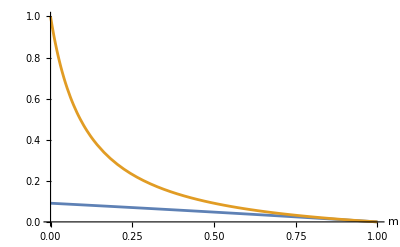

```mathematica
Plot[Evaluate[{(1-m)/(n+1-m),(1-m)/(1+m (-1+n))}/. n->10],{m,0,1},PlotRange->{0,1},AxesLabel->{m}]
```

### Wright Fisher -- Cancellation result

```mathematica
Clear["Global`*"];
```

```mathematica
(* relatedness in WF Model in a monomorphic population *)
r == (1-m)^2 (1/n+(n-1)/n r) ;
Solve[% , r ] //FullSimplify
```

{{r→-(-1+m)^2/(-1+(-2+m) m (-1+n))}}

```mathematica
-(-1+m)^2/(-1+(-2+m) m (-1+n)) == (1-m)^2/(1+(n-1)(2-m) m)  //Simplify
```

True

```mathematica
w = ((1-m)ffocal)/((1-m)( ffocal+fneighbour+(n-2)fRes )/n +m f) + (m ffocal)/f  ;
```

```mathematica
w /. ffocal-> f /. fneighbour -> f  /. fRes-> f //Simplify
```

1

```mathematica
(* scale of competition -- note : same as in Moran *)
(-(n-1)D[w,fneighbour])/D[w,ffocal]  /. ffocal-> f /. fneighbour -> f  /. fRes-> f //FullSimplify  ;

% ==((1-m)^2 (n-1))/(n-(1-m)^2)  //Simplify
```

True

```mathematica
(* Scaled relatedness *)
1/(1- r a) (r-a/(n-1)(1+r(n-2) ) )/. r->(1-m)^2/(1+(n-1)(2-m) m) /. a-> ((1-m)^2 (n-1))/(n-(1-m)^2)  //FullSimplify
```

0

### Reciprocity in well mixed population

#### General selection gradient

```mathematica
Clear["Global`*"];
```

```mathematica
fmut = 1 + δ b a[x,y] - δ c a[y,x]  //Simplify  ; 
fres  = 1 + δ b a[y,x] -δ  c a[x,y]  /.y->x  //Simplify ;
W = fmut/fres  //Simplify
```

(1+b δ a[x,y]-c δ a[y,x])/(1+(b-c) δ a[x,x])

```mathematica
S = D[W,y] /. y-> x  //Simplify   ;
Series[%,{δ,0,1}]  //Normal   ;
% /. δ-> 1  ;

% ==Derivative[1,0][a][x,x]( b λ -c ) /. λ -> (Derivative[0,1][a][x,x])/(Derivative[1,0][a][x,x]) //Simplify
```

True

where λ is the responsiveness coefficient : it quantifies how much a trait change in the mutant elicits a change in the contribution or action of its partner, relative to the change it elicits in its own contribution.

#### The evolution of reciprocity

```mathematica
Clear["Global`*"];
```

```mathematica
(d ay)/dt == a0 - ay + y ax ; 
(d ax)/dt ==a0-ax + x  ay   ;
```

```mathematica
solSys=Flatten@Solve[{ a0 - ay + y ax ==0 ,a0-ax + x  ay   == 0 },{ay,ax}] //Simplify
```

{ay→(a0 (1+y))/(1-x y),ax→(a0 (1+x))/(1-x y)}

{{ax→Function[{t},ⅇ^(-2. t) (-1.3962 ⅇ^(0.683772 t)-11.9371 ⅇ^(1.31623 t)+8.88178×10^-16 ⅇ^(1.36754 t)+13.3333 ⅇ^(2. t)+1.11022×10^-16 ⅇ^(2.63246 t))],ay→Function[{t},16.6667 ⅇ^(-2. t) (0.132456 ⅇ^(0.683772 t)-1.13246 ⅇ^(1.31623 t)+1. ⅇ^(2. t)+1.33227×10^-17 ⅇ^(2.63246 t))]}}

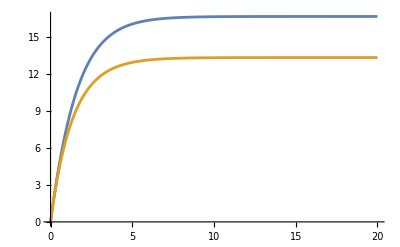

```mathematica
sol = DSolve[{ ay'[t]==a0 - ay[t] + y ax[t]  ,ax'[t]== a0-ax[t] + x  ay[t]  ,ay[0]==0 ,ax[0] ==0  } /.a0->10 /. x->0.2 /.y->0.5 ,{ay,ax},t]
Plot[Evaluate[{ay[t],ax[t]}/.sol /.a-> 10],{t,0,20},PlotRange->All]
```

```mathematica
fmut = 1 + δ b ax - δ c ay /. solSys  //Simplify  ; 
fres  = 1 + δ b  ay -δ  c ax /. solSys   /.y->x //Simplify ;
W = fmut/fres  //Simplify
```

((-1+x) (1-x y+a0 b (1+x) δ-a0 c (1+y) δ))/((1-x y) (-1+x+a0 (-b+c) δ))

```mathematica
S = D[W,y] /. y-> x  //Simplify 
Series[%,{δ,0,1}]
```

(a0 (-c+b x) δ)/((-1+x) (1+x) (-1+x+a0 (-b+c) δ))

(a0 (-c+b x) δ)/((-1+x)^2 (1+x))+O[δ]^2

```mathematica
sing = Flatten@Solve[S ==0,x]
```

{x→c/b}

```mathematica
J = D[S,x] /.sing  //Simplify
```

(a0 b^4 δ)/((b-c)^2 (b+c) (1+a0 b δ))

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]